```mathematica
SetDirectory[NotebookDirectory[]];
Import["FunctionsAndConstants.wl"] ;(* parents directory could be "../LLR/FunctionsAndConstants.wl" etc*)
Needs["NDSolve`FEM`"];
Needs["NumericalCalculus`"];
Needs["MaTeX`"]
Clear[rhoV,ρV,rhoM]
ρV= SetPrecision[1.6726*10^-20*kgm32MeV4,1000];
rhoV=ρV;
rhoM=rhoS;
ρCosmos=2.512792571065065102211739674794535033948495662732724260254001020163981835118*10^-35;
```

## Exclusion plots

```mathematica
ρV= SetPrecision[1.6726*10^-20*kgm32MeV4,1000]; (*roughly density of interplanatery medium*)
ϕρ[A_,λ_,β_,ρ_]:=SetPrecision[mpl/λ If[2*Log10[λ]+β-Log10[A]-Log10[ρ]<10^12,ProductLog[(λ^2 10^β)/(A ρ)],Log[λ^2/(A ρ)]+1/(6 (β Log[10]+Log[λ^2/(A ρ)])^3)(6 β Log[10] (β Log[10]+Log[λ^2/(A ρ)])^3-6 (-1+β Log[10]+Log[λ^2/(A ρ)]) (1+β^2 Log[10]^2+2 β Log[10] Log[λ^2/(A ρ)]+Log[λ^2/(A ρ)]^2) Log[β Log[10]+Log[λ^2/(A ρ)]]+3 (-3+β Log[10]+Log[λ^2/(A ρ)]) Log[β Log[10]+Log[λ^2/(A ρ)]]^2+2 Log[β Log[10]+Log[λ^2/(A ρ)]]^3)],1000]

RangeV[λ_,A2_,β_]:=1/μ[A2,λ,β,ρM]/(ddr/10)

RangeV2[λ_,A2_,β_,ρV2_]:=1/μ[A2,λ,β,ρV2]/(ddr/10)
Q[A2_,λ_,β_,ρM_,ρV_,R_]:=If[μ[A2,λ,β,ρM]*R<100,3/(μ[A2,λ,β,ρM]^2 R^2)(1-1/(μ[A2,λ,β,ρM]*R)Tanh[SetPrecision[μ[A2,λ,β,ρM]*R,1000]])/(1+μ[A2,λ,β,ρV]/μ[A2,λ,β,ρM] Tanh[SetPrecision[μ[A2,λ,β,ρM]*R,1000]]),3/(μ[A2,λ,β,ρM]^2 R^2)(1-1/(μ[A2,λ,β,ρM]*R))/(1+μ[A2,λ,β,ρV]/μ[A2,λ,β,ρM])]
```

### LLRI

```mathematica
(*ϕOUT[A2_,λ_,β_,ρS_,ρV_,R_,r_]:=ϕρ[A2,λ,β,ρV]-Q[A2,λ,β,ρS,ρV,R]*(μ[A2,λ,β,ρS]^2*R^3)/3(ϕρ[A2,λ,β,ρV]-ϕρ[A2,λ,β,ρS])*Exp[-μ[A2,λ,β,ρV]*(r-R)]/r*)

(*aM=-A2*Q[A2,λ,β,ρM,ρV,RM]/mpl^2*FullSimplify[(ϕρ[A2,λ,β,ρV]-Q[A2,λ,β,ρS,ρV,RS]*(μ[A2,λ,β,ρS]^2*RS^3)/3(ϕρ[A2,λ,β,ρV]-ϕρ[A2,λ,β,ρS])*Exp[-μ[A2,λ,β,ρV]*(r-RS)]/r)*D[ϕρ[A2,λ,β,ρV]-Q[A2,λ,β,ρS,ρV,RS]*(μ[A2,λ,β,ρS]^2*RS^3)/3(ϕρ[A2,λ,β,ρV]-ϕρ[A2,λ,β,ρS])*Exp[-μ[A2,λ,β,ρV]*(r-RS)]/r,r]];
aE=-A2 Q[A2,λ,β,ρE,ρV,RE]/mpl^2*FullSimplify[(ϕρ[A2,λ,β,ρV]-Q[A2,λ,β,ρS,ρV,RS]*(μ[A2,λ,β,ρS]^2*RS^3)/3(ϕρ[A2,λ,β,ρV]-ϕρ[A2,λ,β,ρS])*Exp[-μ[A2,λ,β,ρV]*(r-RS)]/r)*D[ϕρ[A2,λ,β,ρV]-Q[A2,λ,β,ρS,ρV,RS]*(μ[A2,λ,β,ρS]^2*RS^3)/3(ϕρ[A2,λ,β,ρV]-ϕρ[A2,λ,β,ρS])*Exp[-μ[A2,λ,β,ρV]*(r-RS)]/r,r]];*)
```

$Aborted

$Aborted

```mathematica
(*FullSimplify[(aM-aE)/aG]/.{r->RES}*)
```

-1/(9 aG mpl^2 RES^3)A2 ⅇ^((-RES+RS) μ[A2,λ,β,ρV]) RS^3 (Q[A2,λ,β,ρE,ρV,RE]-Q[A2,λ,β,ρM,ρV,RM]) Q[A2,λ,β,ρS,ρV,RS] μ[A2,λ,β,ρS]^2 (1+RES μ[A2,λ,β,ρV]) (ϕρ[A2,λ,β,ρS]-ϕρ[A2,λ,β,ρV]) (ⅇ^((-RES+RS) μ[A2,λ,β,ρV]) RS^3 Q[A2,λ,β,ρS,ρV,RS] μ[A2,λ,β,ρS]^2 (ϕρ[A2,λ,β,ρS]-ϕρ[A2,λ,β,ρV])+3 RES ϕρ[A2,λ,β,ρV])

```mathematica
δem[A2_,λ_,β_]:=If[(A2*ϕρ[A2,λ,β,ρV]^2)/(2*mpl^2)>=0.1,0,Abs[-1/(9 aG mpl^2 RES^3)A2 ⅇ^((-RES+RS) μ[A2,λ,β,ρV]) RS^3 (Q[A2,λ,β,ρE,ρV,RE]-Q[A2,λ,β,ρM,ρV,RM]) Q[A2,λ,β,ρS,ρV,RS] μ[A2,λ,β,ρS]^2 (1+RES μ[A2,λ,β,ρV]) (ϕρ[A2,λ,β,ρS]-ϕρ[A2,λ,β,ρV]) (ⅇ^((-RES+RS) μ[A2,λ,β,ρV]) RS^3 Q[A2,λ,β,ρS,ρV,RS] μ[A2,λ,β,ρS]^2 (ϕρ[A2,λ,β,ρS]-ϕρ[A2,λ,β,ρV])+3 RES ϕρ[A2,λ,β,ρV])]]

δemCosmos[A2_,λ_]:=If[ (A2*ϕρ[A2,λ,Log10[V0[A2,λ]],ρCosmos]^2)/(2*mpl^2) >=0.1,0,Abs[-1/(9 aG mpl^2 RES^3)A2 ⅇ^((-RES+RS) μ[A2,λ,Log10[V0[A2,λ]],ρV]) RS^3 (Q[A2,λ,Log10[V0[A2,λ]],ρE,ρV,RE]-Q[A2,λ,Log10[V0[A2,λ]],ρM,ρV,RM]) Q[A2,λ,Log10[V0[A2,λ]],ρS,ρV,RS] μ[A2,λ,Log10[V0[A2,λ]],ρS]^2 (1+RES μ[A2,λ,Log10[V0[A2,λ]],ρV]) (ϕρ[A2,λ,Log10[V0[A2,λ]],ρS]-ϕρ[A2,λ,Log10[V0[A2,λ]],ρV]) (ⅇ^((-RES+RS) μ[A2,λ,Log10[V0[A2,λ]],ρV]) RS^3 Q[A2,λ,Log10[V0[A2,λ]],ρS,ρV,RS] μ[A2,λ,Log10[V0[A2,λ]],ρS]^2 (ϕρ[A2,λ,Log10[V0[A2,λ]],ρS]-ϕρ[A2,λ,Log10[V0[A2,λ]],ρV])+3 RES ϕρ[A2,λ,Log10[V0[A2,λ]],ρV])]]
```

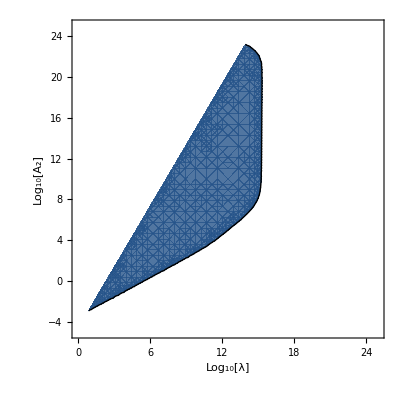

```mathematica
Clear[Y,β]
β=1;
Y=ColorData["M10DefaultDensityGradient"]@(0.8*0/27);
LLRB2Alt=ContourPlot[δem[10^y,10^x,β]*10^13/2,{x,Log10[10^0],Log10[10^25]},{y,Log10[10^-5],Log10[10^25]},FrameLabel->{"Log_10[λ]","Log_10[A_2]"},Contours-> {{1}},ContourShading->{Opacity[0.01,White],Opacity[0.8,Y]},PlotRange->All,ContourStyle->Directive[Y,Thick,Black],PlotTheme->None]
```

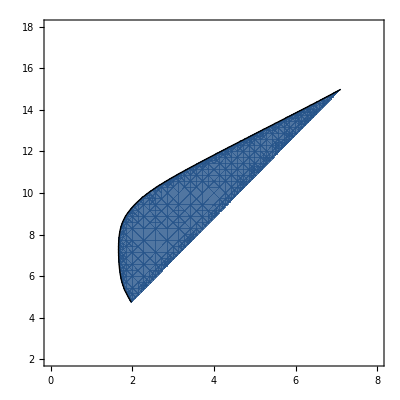

```mathematica
Clear[Y,β]
Y=ColorData["M10DefaultDensityGradient"]@(0.8*0/27);
LLRI=ContourPlot[δemCosmos[10^y,10^x]*10^13/2,{x,Log10[10^0],Log10[10^8]},{y,Log10[10^2],Log10[10^18]}(*,FrameLabel->{"Log_10[  ]","Log_10[A_2]"*),Contours-> {{1}},ContourShading->{Opacity[0.01,White],Opacity[0.8,Y]},PlotRange->All,ContourStyle->Directive[Y,Thick,Black],PlotTheme->None,LabelStyle->{FontFamily->"Arial", FontSize->13},FrameLabel->(MaTeX[#,Magnification->1.2]&/@{"\\log_{10}[\\lambda]","\\log_{10}[A_2]"})]
```

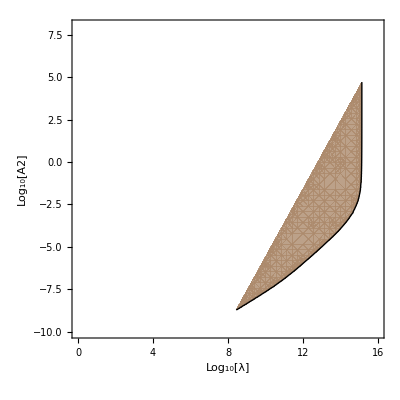

```mathematica
Clear[Y,β]
β=10^12;
Y=ColorData["M10DefaultDensityGradient"]@(0.8*12/27);
LLRB2Alt2=ContourPlot[δem[10^y,10^x,β]*10^13/2,{x,Log10[10^0],Log10[10^16]},{y,Log10[10^-10],Log10[10^8]},FrameLabel->{"Log_10[λ]","Log_10[A2]"},Contours-> {{1}},ContourShading->{Opacity[0.01,White],Opacity[0.8,Y]},PlotRange->All,ContourStyle->Directive[Y,Thick,Black],PlotTheme->None]
```

### LLRII

```mathematica
ρV= SetPrecision[1.6726*10^-20*kgm32MeV4,1000]; (*roughly density of interplanatery medium*)
δf [r_,A2_,λ_, β_]:=1/(9 mpl^2 r^3)A2 ⅇ^(2 (-r+RE) μ[A2,λ,β,ρV]) RE^3 Q[A2,λ,β,ρE,ρV,RE] Q[A2,λ,β,ρM,ρV,RM] μ[A2,λ,β,ρE]^2 (1+r μ[A2,λ,β,ρV]) (ϕρ[A2,λ,β,ρE]-ϕρ[A2,λ,β,ρV]) (RE^3 Q[A2,λ,β,ρE,ρV,RE] μ[A2,λ,β,ρE]^2 (ϕρ[A2,λ,β,ρE]-ϕρ[A2,λ,β,ρV])+3 ⅇ^((r-RE) μ[A2,λ,β,ρV]) r ϕρ[A2,λ,β,ρV])

ϕ[A2_,λ_,β_,r_]:=-ϕρ[A2,λ,β,ρV]-Q[A2,λ,β,ρE,ρV,RE]*(μ[A2,λ,β,ρE]^2*RE^3)/3(ϕρ[A2,λ,β,ρV]-ϕρ[A2,λ,β,ρE])*Exp[-μ[A2,λ,β,ρV]*(r-RE)]/r

ϕρ[A_,λ_,β_,ρ_]:=SetPrecision[mpl/λ If[2*Log10[λ]+β-Log10[A]-Log10[ρ]<50,ProductLog[(λ^2 10^β)/(A ρ)],Log[λ^2/(A ρ)]+1/(6 (β Log[10]+Log[λ^2/(A ρ)])^3)(6 β Log[10] (β Log[10]+Log[λ^2/(A ρ)])^3-6 (-1+β Log[10]+Log[λ^2/(A ρ)]) (1+β^2 Log[10]^2+2 β Log[10] Log[λ^2/(A ρ)]+Log[λ^2/(A ρ)]^2) Log[β Log[10]+Log[λ^2/(A ρ)]]+3 (-3+β Log[10]+Log[λ^2/(A ρ)]) Log[β Log[10]+Log[λ^2/(A ρ)]]^2+2 Log[β Log[10]+Log[λ^2/(A ρ)]]^3)],1000]

RangeV[λ_,A2_,β_]:=1/μ[A2,λ,β,ρM]/(ddr/10)

RangeV2[λ_,A2_,β_,ρV2_]:=1/μ[A2,λ,β,ρV2]/(ddr/10)
Q[A2_,λ_,β_,ρM_,ρV_,R_]:=If[μ[A2,λ,β,ρM]*R<100,3/(μ[A2,λ,β,ρM]^2 R^2)(1-1/(μ[A2,λ,β,ρM]*R)Tanh[SetPrecision[μ[A2,λ,β,ρM]*R,1000]])/(1+μ[A2,λ,β,ρV]/μ[A2,λ,β,ρM] Tanh[SetPrecision[μ[A2,λ,β,ρM]*R,1000]]),3/(μ[A2,λ,β,ρM]^2 R^2)(1-1/(μ[A2,λ,β,ρM]*R))/(1+μ[A2,λ,β,ρV]/μ[A2,λ,β,ρM])]


δΩdΩ[A2_,λ_, β_]:=If[(A2*ϕρ[A2,λ,β,ρV]^2)/(2*mpl^2)>=0.1,0,Abs[-1/(18 GN ME mpl^2 REM)A2 ⅇ^((RE-REM) μ[A2,λ,β,ρV]) RE^3 Q[A2,λ,β,ρE,ρV,RE] Q[A2,λ,β,ρM,ρV,RM] μ[A2,λ,β,ρE]^2 (ϕρ[A2,λ,β,ρE]-ϕρ[A2,λ,β,ρV]) (ⅇ^((RE-REM) μ[A2,λ,β,ρV]) RE^3 Q[A2,λ,β,ρE,ρV,RE] μ[A2,λ,β,ρE]^2 (1+2 REM μ[A2,λ,β,ρV] (1+REM μ[A2,λ,β,ρV])) (ϕρ[A2,λ,β,ρE]-ϕρ[A2,λ,β,ρV])+3 REM^3 μ[A2,λ,β,ρV]^2 ϕρ[A2,λ,β,ρV])]]

δΩdΩCosmos[A2_,λ_]:=If[ (A2*ϕρ[A2,λ,Log10[V0[A2,λ]],ρCosmos]^2)/(2*mpl^2) >=0.1,0,Abs[-1/(18 GN ME mpl^2 REM)A2 ⅇ^((RE-REM) μ[A2,λ,Log10[V0[A2,λ]],ρV]) RE^3 Q[A2,λ,Log10[V0[A2,λ]],ρE,ρV,RE] Q[A2,λ,Log10[V0[A2,λ]],ρM,ρV,RM] μ[A2,λ,Log10[V0[A2,λ]],ρE]^2 (ϕρ[A2,λ,Log10[V0[A2,λ]],ρE]-ϕρ[A2,λ,Log10[V0[A2,λ]],ρV]) (ⅇ^((RE-REM) μ[A2,λ,Log10[V0[A2,λ]],ρV]) RE^3 Q[A2,λ,Log10[V0[A2,λ]],ρE,ρV,RE] μ[A2,λ,Log10[V0[A2,λ]],ρE]^2 (1+2 REM μ[A2,λ,Log10[V0[A2,λ]],ρV] (1+REM μ[A2,λ,Log10[V0[A2,λ]],ρV])) (ϕρ[A2,λ,Log10[V0[A2,λ]],ρE]-ϕρ[A2,λ,Log10[V0[A2,λ]],ρV])+3 REM^3 μ[A2,λ,Log10[V0[A2,λ]],ρV]^2 ϕρ[A2,λ,Log10[V0[A2,λ]],ρV])]]
```

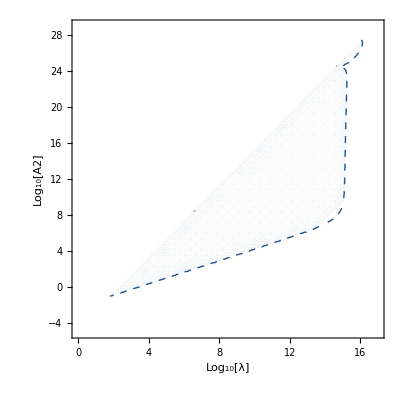

```mathematica
Clear[Y,β]
β=1;
Y=ColorData["M10DefaultDensityGradient"]@(0.8*0/27);
LLRALT=ContourPlot[Abs[δΩdΩ[10^A,10^λ,β]]/(6.23833*10^-12),{λ,Log10[10^0],Log10[10^17]},{A,Log10[10^-5],Log10[10^29]},FrameLabel->{"Log_10[λ]","Log_10[A2]"},Contours-> {1},ContourShading->{Opacity[0.01,White],Opacity[0.01,Y]},PlotRange->All,ContourStyle->Directive[Y,Thick,Dashed],PlotTheme->None]
```

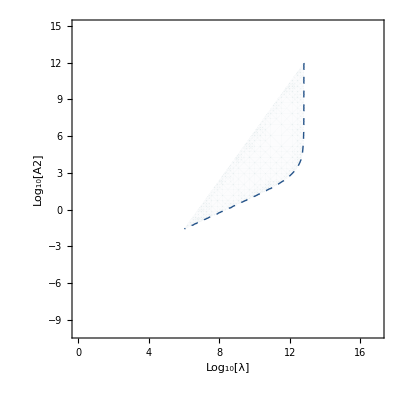

```mathematica
Clear[Y,β]
β=10^6;
Y=ColorData["M10DefaultDensityGradient"]@(0.8*0/27);
LLRALT=ContourPlot[Abs[δΩdΩ[10^A,10^λ,β]]/SetPrecision[6.23833*10^-12,100],{λ,Log10[10^0],Log10[10^17]},{A,Log10[10^-10],Log10[10^15]},FrameLabel->{"Log_10[λ]","Log_10[A2]"},Contours-> {1},ContourShading->{Opacity[0.01,White],Opacity[0.01,Y]},PlotRange->All,ContourStyle->Directive[Y,Thick,Dashed],PlotTheme->None]
```

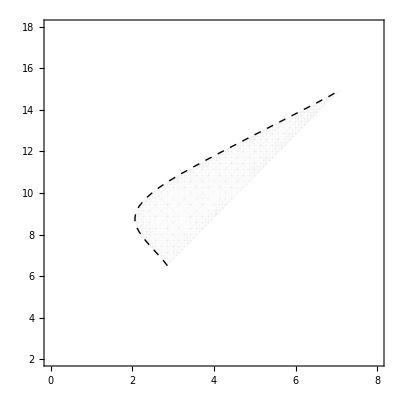

```mathematica
Clear[Y,β]
Y=ColorData["M10DefaultDensityGradient"]@(0.8*0/27);
LLRII=ContourPlot[Abs[δΩdΩCosmos[10^A,10^λ]]/(6.23833*10^-12),{λ,Log10[10^0],Log10[10^8]},{A,Log10[10^2],Log10[10^18]},Contours-> {1},ContourShading->{Opacity[0.01,White],Opacity[0.01,Black]},PlotRange->All,ContourStyle->Directive[Black,Thick,Dashed],PlotTheme->None,LabelStyle->{FontFamily->"Arial", FontSize->13},FrameLabel->(MaTeX[#,Magnification->1.2]&/@{"\\log_{10}[\\lambda]","\\log_{10}[A_2]"})]
```

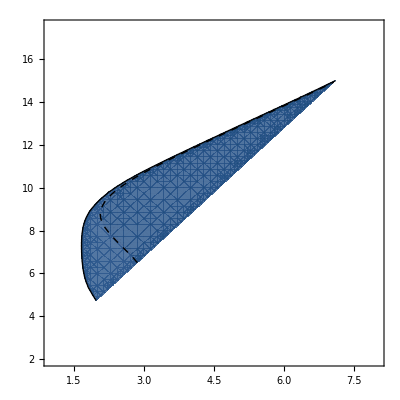

```mathematica
COSMOS=Show[LLRI,LLRII,PlotRange->{{1,8},{2,17.5}}]
```

```mathematica
Export["Cosmos.pdf",COSMOS]
```

Cosmos.pdf

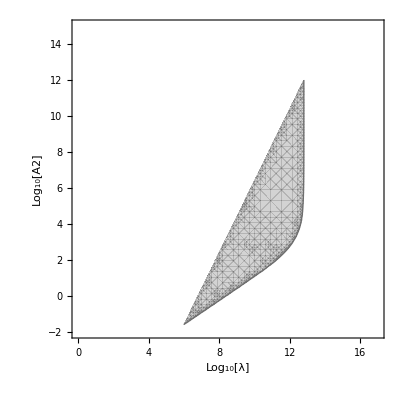

```mathematica
β=10^6;
Y=RGBColor[110/255,110/255,110/255];
LLRB2=ContourPlot[Abs[δΩdΩ[10^A,10^λ,β]]/(6.23833*10^-12),{λ,Log10[10^0],Log10[10^17]},{A,Log10[10^-2],Log10[10^15]},FrameLabel->{"Log_10[λ]","Log_10[A2]"},Contours-> {1},ContourShading->{Opacity[0.01,White],Opacity[0.3,Y]},PlotRange->All,ContourStyle->Directive[Y,Thick],PlotTheme->None,WorkingPrecision->100]
```